Symbolic integration of the cosine-weighted constant visibility function ∫cosθ sinθⅆθ= -1/2 cos^2 θ
Integration over the entire hemisphere ∫_0^(2π) ∫_0^(π/2) cosθ sinθⅆθⅆϕ=π

```mathematica
2π * Integrate[Cos[θ]Sin[θ],{θ,0,π/2}]
```

π

We can then assume that the Ambient Occlusion value of a flat, unoccluded surface should equal π, which is then scaled to 1 to be stored into a classical AO texture.
So let’s decide that an AO map’s value should be scaled by π when read by a shader, multiplied by ρ/πthe surface’s albedo to obtain a [0,1] ambient reflectance value, then multiplied by the irradiance perceived by the surface to finally obtain the reflected radiance in the outgoing direction ω_o:
	L(x,ω_o) = ρ/π (π AO)E(x)=ρ AO E(x)

We can write the “direct” irradiance estimate as:
	E_0(x)=∫_Ω^□ L_0 V_dir(ω_i)(n.ω_i)ⅆ ω_i
Where L_0=1 and V_dir(ω_i) represents the direct visibility function that equals 1 if the ray is unoccluded by the surface, 0 otherwise.
We notice that E_0(x) is exactly the value computed for the Ambient Occlusion, so E_0(x)=AO.

We can then write the general expression for the “indirect” irradiance estimate as:
	E_(n+1)(x)=∫_Ω^□ L_i(x,ω_i )V_ind(ω_i)(n.ω_i)ⅆ ω_i
Where V_ind(ω_i) represents the indirect visibility function that equals 1 if the ray is occluded by the surface, 0 otherwise (so V_ind(ω_i)=1-V_dir(ω_i) ).
We can rewrite the perceived incoming luminance L_i(x,ω_i ) from a neighbor location x' as:
	L_i(x,ω_i )=ρ/π E_n(x')
And finally:
	E_(n+1)(x)=∫_Ω^□ ρ/π E_n(x')V_ind(ω_i)(n.ω_i)ⅆ ω_i

We easily see that we can compute the irradiance incrementally by re-using the previous irradiance at the indirect neighbor locations.

## Fitting Experimental Data

After writing the program that computes the AO and the multiple indirect bounces from a height map, we collect the bounced illuminance values into histograms where the bin indices are given by the AO values: this bascially computes the average indirect illuminance perceived by a point given its AO value (AO value is in [0,π] but we rescaled it to [0,1] for convenience).
We do that for multiple bounces to try and find a pattern in the shape and amplitude of the curves...

To generate the curves shown below, we used the WallHeight.png as a height map, and its corresponding WallNormal.png as a normal map.
We also chose a height value of 5 cm for a total wall length of 1 meter, 1024 rays at 179° cone aperture.
It gave some nice curves without the annoying artefacts found at the extremas that can be found with other maps.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]; 
tableSize = 100;
bouncesCount = 10;
rawArray=Table[ BinaryReadList["WallHeight"<>ToString[i]<>".float", "Real32"],{i,1,bouncesCount}];
bounces = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
```

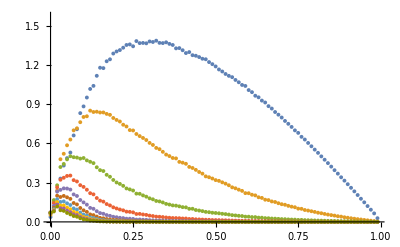

```mathematica
ListPlot[bounces,PlotRange->{0,π/2}]
```

Intuitively, it looks more and more like a normal distribution and we can model it as f(x)=a*x*(1-x)*e^-bx.
We can see below that it’s actually a very nice fit for the curves and may even deduce a general rule to find a and b coefficients as a function of the bounce index...

```mathematica
Manipulate[Plot[8*x*(1-x)*ⅇ^(-k*x),{x,0,1},PlotRange->{0,π/2}],{{k,1},0,20}]
```

```mathematica
Clear[a,b]
model=b/a*x*(1-x)*Exp[-b*x];
fitter[i_]:=Module[{},
FindFit[bounces[[i]], model,{a,{b,20}},{x}]
]
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}]
```

{{a→0.145266,b→1.55043},{a→0.360125,b→4.9367},{a→0.662865,b→9.62783},{a→1.00588,b→16.3854},{a→1.36116,b→22.712},{a→1.74407,b→27.4423},{a→2.15167,b→31.166},{a→2.57505,b→34.4689},{a→3.00497,b→37.6836},{a→3.43309,b→40.9832}}

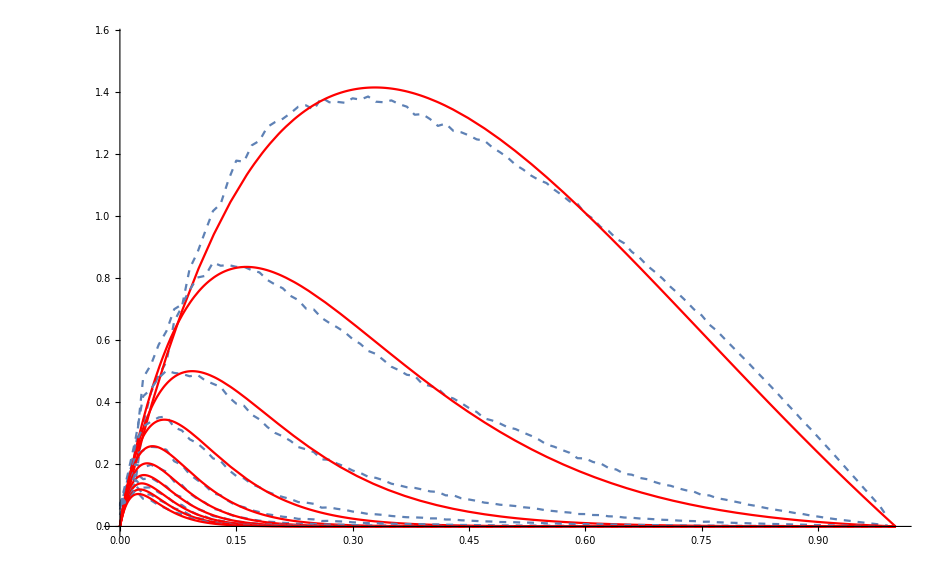

```mathematica
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.fits[[bounceIndex]],{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

Now we plot the various a and b coefficients as a function of the bounce index:

{0.145266,0.360125,0.662865,1.00588,1.36116,1.74407,2.15167,2.57505,3.00497,3.43309}

{1.55043,4.9367,9.62783,16.3854,22.712,27.4423,31.166,34.4689,37.6836,40.9832}

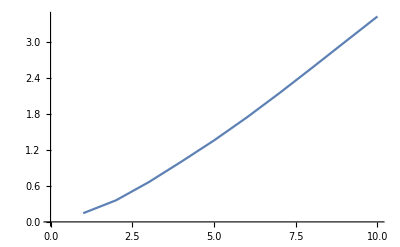

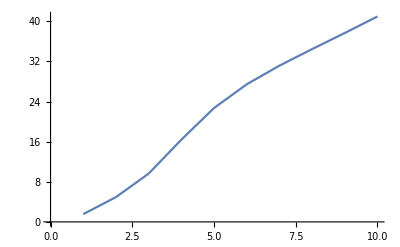

```mathematica
coeffsA=Table[a/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
coeffsB=Table[b/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
ListLinePlot[coeffsA,PlotRange->Full]
ListLinePlot[coeffsB,PlotRange->Full]
```

We notice the curves are almost linear so let’s try and fit the a and b coefficients as a linear function of the bounce index:

{a0→-0.0324635,a1→0.372639}

{b0→0.,b1→4.66749}

Function[{x},-0.0324635+0.372639 (-1+x)]

Function[{x},1.55043+4.66749 (-1+x)]

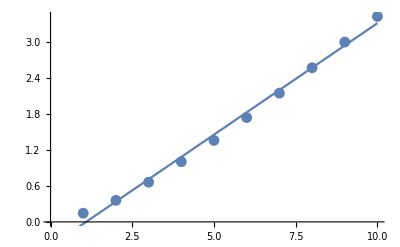

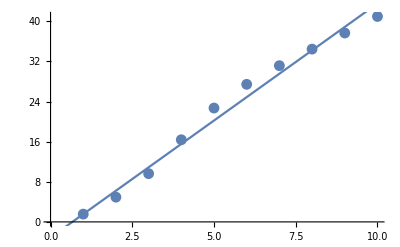

```mathematica
modelA=0*0.14526642906187737+a0+a1*(x-1);
modelB=1.5504282580946984+0*b0+b1*(x-1);
modelFitA=FindFit[coeffsA,modelA,{a0,a1},{x}]
modelFitB=FindFit[coeffsB,modelB,{b0,b1},{x}]
(*Show[ListPlot[coeffsA,PlotRange->Full],Plot[modelA/.modelFitA,{x,0,bouncesCount}]]
Show[ListPlot[coeffsB,PlotRange->Full],Plot[modelB/.modelFitB,{x,0,bouncesCount}]]*)

modelFitA=Function[{x},Evaluate[modelA/.modelFitA]]
modelFitB=Function[{x},Evaluate[modelB/.modelFitB]]
Show[ListPlot[coeffsA,PlotRange->Full],Plot[modelFitA[x],{x,0,bouncesCount}]]
Show[ListPlot[coeffsB,PlotRange->Full],Plot[modelFitB[x],{x,0,bouncesCount}]]
```

```mathematica
a-> modelFitA[1]
```

a→0.145266

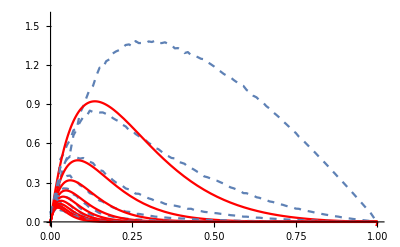

```mathematica
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.{a-> modelFitA[bounceIndex],b-> modelFitB[bounceIndex]},{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

## Refitting with Constrained b

Assuming b= 1.5504282580946984+0*b0 + b1*(bounceIndex-1) we can try and re-fit the remaining variable a:

```mathematica
fitter[i_]:=Module[{},
b = modelFitB[i];
FindFit[bounces[[i]], model,{a},{x}]
];
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}];
coeffsA=Table[a/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
```

{0.145266,0.348289,0.638006,1.02784,1.43638,1.82668,2.2058,2.58354,2.96244,3.34059}

{a0→-0.372144,a1→0.367932}

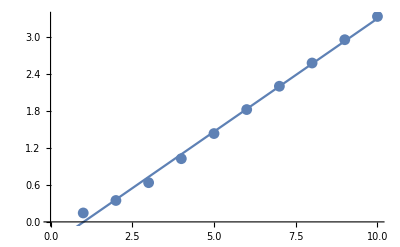

```mathematica
modelA=a0+a1*x;
modelFitA=FindFit[coeffsA,modelA,{a0,a1},{x}]
modelFitA=Function[{x},Evaluate[modelA/.modelFitA]];
Show[ListPlot[coeffsA,PlotRange->Full],Plot[modelFitA[x],{x,0,bouncesCount}]]
```

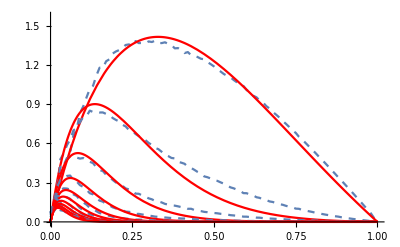

```mathematica
Clear[a,b]
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.{ a-> coeffsA[[bounceIndex]],b->modelFitB[bounceIndex]},{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

## Using Fitted Data

qsd

{a→6.8839,b→1.55043}

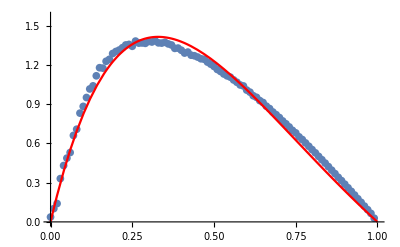

```mathematica
modelFit1=FindFit[bounces[[1]], model,{a,b},{x}]
bounce1=Function[{x},Evaluate[model/.modelFit1]];
Show[
ListPlot[bounces[[1]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce1[x],{x,0,1},PlotStyle->Red]
]
```

{a→2.77681,b→4.9367}

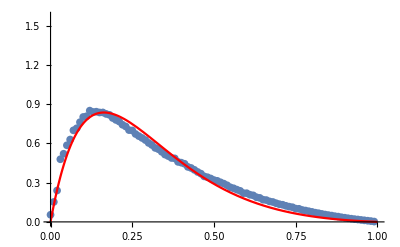

```mathematica
modelFit2=FindFit[bounces[[2]], model,{a,b},{x}]
bounce2=Function[{x},Evaluate[model/.modelFit2]];
Show[
ListPlot[bounces[[2]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce2[x],{x,0,1},PlotStyle->Red]
]
```

{a→1.5086,b→9.62783}

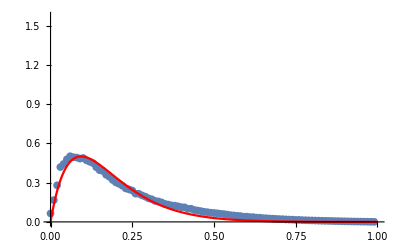

```mathematica
modelFit3=FindFit[bounces[[3]], model,{a,b},{x}]
bounce3=Function[{x},Evaluate[model/.modelFit3]];
Show[
ListPlot[bounces[[3]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce3[x],{x,0,1},PlotStyle->Red]
]
```

{a→0.994155,b→16.3854}

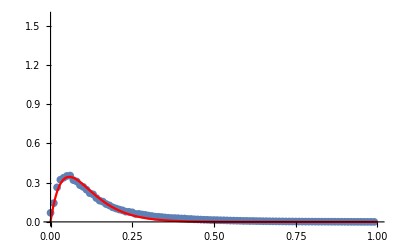

```mathematica
modelFit4=FindFit[bounces[[4]], model,{a,b},{x}]
bounce4=Function[{x},Evaluate[model/.modelFit4]];
Show[
ListPlot[bounces[[4]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce4[x],{x,0,1},PlotStyle->Red]
]
```

{6.8839,2.77681,1.5086,0.994155}

{1.55043,4.9367,9.62783,16.3854}

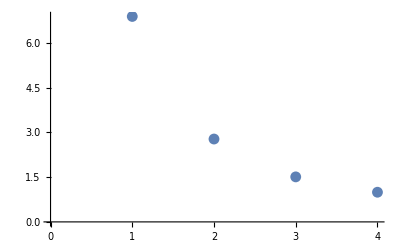

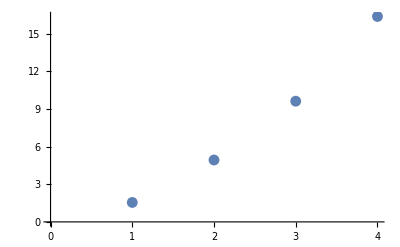

```mathematica
coeffsA={a/.modelFit1,a/.modelFit2,a/.modelFit3,a/.modelFit4}
coeffsB={b/.modelFit1,b/.modelFit2,b/.modelFit3,b/.modelFit4}
ListPlot[coeffsA]
ListPlot[coeffsB]
```